# L4 Shape function and Derivates

## Isoparametric Formulation of Shape functions:

```mathematica
Quit[];
```

### L4 element

Based on linear polynomial, u^e(x_) = α_0^e+α_1^e x+α_2^e x^2+α_3^e x^3

```mathematica
coef = ({{Subscript[α, 0]}, {Subscript[α, 1]}, {Subscript[α, 2]}, {Subscript[α, 3]}});
p[x_]:= ({{1, x, x^2, x^3}})
M= ({{1, Subscript[x, 1], Subscript[x, 1]^2, Subscript[x, 1]^3}, {1, Subscript[x, 2], Subscript[x, 2]^2, Subscript[x, 2]^3}, {1, Subscript[x, 3], Subscript[x, 3]^2, Subscript[x, 3]^3}, {1, Subscript[x, 4], Subscript[x, 4]^2, Subscript[x, 4]^3}});
```

```mathematica
u=  p[x].coef
```

(α_3 x^3+α_2 x^2+α_1 x+α_0)

```mathematica
Ne[x_]:= p[x].Inverse[M]
```

```mathematica
Ne[x] //Simplify
```

(((x-x_2) (x-x_3) (x-x_4))/((x_1-x_2) (x_1-x_3) (x_1-x_4)) | -((x-x_1) (x-x_3) (x-x_4))/((x_1-x_2) (x_2-x_3) (x_2-x_4)) | -((x-x_1) (x-x_2) (x-x_4))/((x_1-x_3) (x_3-x_2) (x_3-x_4)) | -((x-x_1) (x-x_2) (x-x_3))/((x_1-x_4) (x_4-x_2) (x_4-x_3)))

### Test L4 element

```mathematica
Ne[Subscript[x, 1]]//Simplify
Ne[Subscript[x, 2]]//Simplify
Ne[Subscript[x, 3]]//Simplify
Ne[Subscript[x, 4]]//Simplify
```

(1 | 0 | 0 | 0)

(0 | 1 | 0 | 0)

(0 | 0 | 1 | 0)

(0 | 0 | 0 | 1)

```mathematica
n = Dimensions[Ne[x]]
```

{1,4}

```mathematica
Sum[Ne[x][[1,i]],{i,1,4}] //Simplify
```

1

### L4 Isoparametric Formulation

```mathematica
(* set Subscript[x, 4]-Subscript[x, 1] = l^e, Subscript[x, 2]-Subscript[x, 1] = l^e/3, Subscript[x, 3]-Subscript[x, 2] = l^e/3 and choose l^e= 2ξ
 such that ξ(Subscript[x, 1])= -1 , ξ(Subscript[x, 2])= 0 and ξ(Subscript[x, 3])= 1 *)
(* ξ=(Subscript[x, 3]+Subscript[x, 2])/2+(Subscript[x, 3]-Subscript[x, 2])/2 x *)
```

```mathematica
x-Subscript[x, 4]= ξ-1
x-Subscript[x, 3]= ξ-2/3
x-Subscript[x, 2]= ξ+2/3
x-Subscript[x, 1]= ξ+1
```

```mathematica
Ne[x]  .Subscript[x, 4]-> 1-ξ+x/.Subscript[x, 3]-> 1/3-ξ+x/.Subscript[x, 2]-> -1/3-ξ+x/.Subscript[x, 1]-> -1-ξ+x//Simplify
```

(-((9 ξ^2-1) (x-x_4))/(8 (ξ-x+x_4+1)) | (9 (3 ξ^2+2 ξ-1) (x-x_4))/(4 (3 ξ-3 x+3 x_4+1)) | (9 (3 ξ^2+4 ξ+1) (x-x_4))/(8 (-3 ξ+3 x-3 x_4+1)) | (-9 ξ^3-9 ξ^2+ξ+1)/(-9 ξ^3-9 ξ^2+ξ+9 x^3+x_4 (-27 ξ^2-18 ξ-27 x^2+18 (3 ξ+1) x+1)-9 (3 ξ+1) x^2+(27 ξ^2+18 ξ-1) x+9 x_4^2 (-3 ξ+3 x-1)-9 x_4^3+1)).x_4→-ξ+x+1

```mathematica
NL3[ξ_]:=  ({{1/2(ξ-1)ξ, 1-ξ^2, 1/2(ξ+1)ξ}})
```

### Test L4 Isoparametric Formulation

```mathematica
NL3[-1]
NL3[0]
NL3[1]
```

(1 | 0 | 0)

(0 | 1 | 0)

(0 | 0 | 1)

```mathematica
Sum[NL3[ξ][[1,i]],{i,1,3}] //Simplify
```

1

### Plot isoparametric shape functions

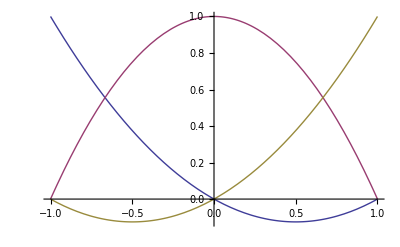

```mathematica
Plot[Tooltip[{NL3[ξ][[1,1]],NL3[ξ][[1,2]],NL3[ξ][[1,3]]}],{ξ,-1,1}]
```